# Filling factor of solenoid

```mathematica
DrawRec[a_,L_]:=Graphics[{EdgeForm[Thin],Transparent,Rectangle[{-a,-L/2},{a,L/2}]}]
```

```mathematica
Aup[a_,L_,ρ_,z_]:=1/(8 ρ √((L-2 z)^2+4 (a+ρ)^2))(L-2 z) (((L-2 z)^2+4 (a+ρ)^2) EllipticE[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]-(8 a^2+(L-2 z)^2+8 ρ^2) EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]+4 (a-ρ)^2 EllipticPi[(4 a ρ)/(a+ρ)^2,(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])
```

## Single NMR Coil

```mathematica
Aϕ[a_,L_,ρ_,z_]:=(*(μ0 i)/(4π)*)(*M*)(Aup[a,L/2,ρ,z]-Aup[a,-L/2,ρ,z])
```

```mathematica
Show[
ContourPlot[Aϕ[1,1,R,Z],{R,-2,2},{Z,-2,2},Contours->Table[0.2n,{n,-15,15}],ContourLabels->True,Exclusions->{R==0}],
DrawRec[1,1]
]
```

### On axis

```mathematica
Fill[a_,L_,R_,k_]:=-2π R (Aup[a,L/2,R,k]-Aup[a,-L/2,R,k])
```

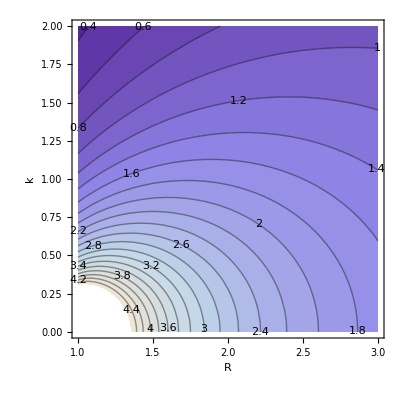

```mathematica
ContourPlot[Fill[1,1,R,k],{R,1,3},{k,0,2},Contours->Table[0.2n,{n,0,40}],ContourLabels->True,FrameLabel->Automatic]
```

```mathematica
ContourPlot3D[-2π R (Aup[1,L/2,R,k]-Aup[1,-L/2,R,k]),{R,1,3},{k,0,2},{L,0.2,2},PlotPoints->6, Contours->Table[n,{n,0,20}]]
```

-Graphics3D-

### Off axis

```mathematica
Filloff[a_,L_,R_,h_,k_]:=-2π R NIntegrate[(Aup[a,L/2,√(h^2+R^2+2 h R Cos[θ]),k]-Aup[a,-L/2,√(h^2+R^2+2 h R Cos[θ]),k]),{θ,0,2π}]
```

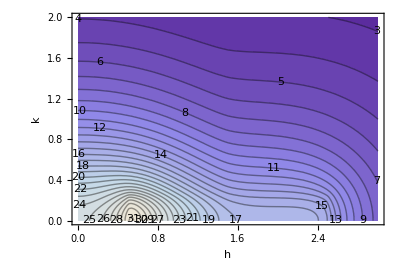

```mathematica
ContourPlot[Filloff[1,0.2,1.5,h,k],{h,0,3},{k,0,2},Contours->Table[n,{n,0,40}],ContourLabels->True,FrameLabel->Automatic,AspectRatio->2/3]
```

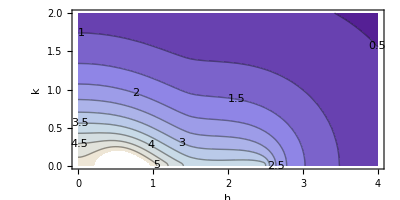

```mathematica
ContourPlot[Filloff[1,0.2,1.5,h,k],{h,0,4},{k,0,2},Contours->Table[0.5n,{n,0,40}],ContourLabels->True,FrameLabel->Automatic,AspectRatio->2/4]
```

## Mutli NMR Coil

```mathematica
(* d is speration distance, n = number of coils *)
(* total lentgh , g=(n-1)d *)
```

```mathematica
FillonSum[a_,L_,R_,d_,n_?NumberQ,k_]:= Sum[-2π R (Aup[a,L/2,R,k+(i-1)d- (n-1)d/2 ]-Aup[a,-L/2,R,k+(i-1)d- (n-1)d/2 ]),{i,1,n}]
```

```mathematica
FilloffSum[a_,L_,R_,d_,n_?NumberQ,h_,k_]:=2Sum[NIntegrate[-2π R (Aup[a,L/2,√(h^2+R^2+2 h R Cos[θ]),k+(i-1)d- (n-1)d/2]-Aup[a,-L/2,√(h^2+R^2+2 h R Cos[θ]),k+(i-1)d- (n-1)d/2]),{θ,0,π}],{i,1,n}]
```

```mathematica
FilloffSum[1,1,1.5,
```

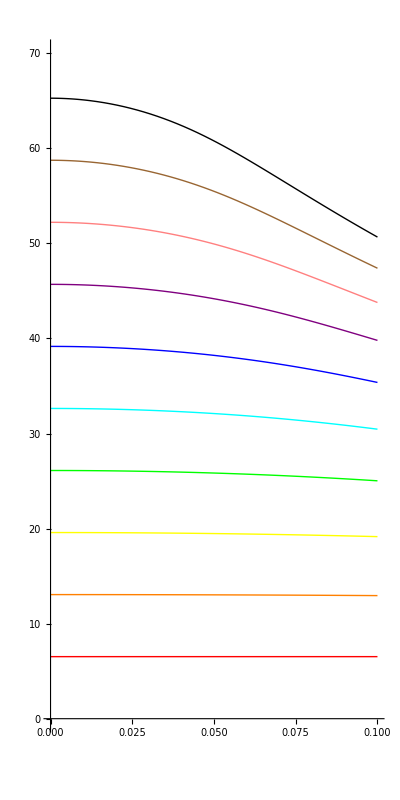

```mathematica
Plot[
{FillonSum[1,1,1.1,d,1,0],
FillonSum[1,1,1.1,d,2,0],
FillonSum[1,1,1.1,d,3,0],
FillonSum[1,1,1.1,d,4,0],
FillonSum[1,1,1.1,d,5,0],
FillonSum[1,1,1.1,d,6,0],
FillonSum[1,1,1.1,d,7,0],
FillonSum[1,1,1.1,d,8,0],
FillonSum[1,1,1.1,d,9,0],
FillonSum[1,1,1.1,d,10,0]
},{d,0,0.1},AspectRatio->4/2,PlotStyle->{Red,Orange, Yellow, Green, Cyan, Blue, Purple, Pink, Brown, Black}, PlotRange->{0,70}]
```

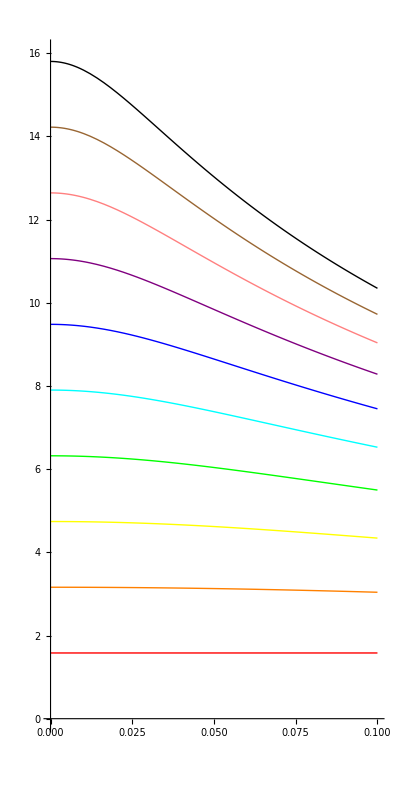

```mathematica
Plot[
{FillonSum[1,0.2,1.1,d,1,0],
FillonSum[1,0.2,1.1,d,2,0],
FillonSum[1,0.2,1.1,d,3,0],
FillonSum[1,0.2,1.1,d,4,0],
FillonSum[1,0.2,1.1,d,5,0],
FillonSum[1,0.2,1.1,d,6,0],
FillonSum[1,0.2,1.1,d,7,0],
FillonSum[1,0.2,1.1,d,8,0],
FillonSum[1,0.2,1.1,d,9,0],
FillonSum[1,0.2,1.1,d,10,0]
},{d,0,0.1},AspectRatio->4/2,PlotStyle->{Red,Orange, Yellow, Green, Cyan, Blue, Purple, Pink, Brown, Black}, PlotRange->{0,16}]
```

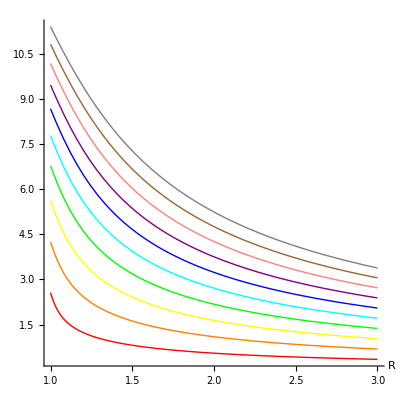

```mathematica
Plot[
{FillonSum[1,0.2,R,0.1,1,0],
FillonSum[1,0.2,R,0.1,2,0],
FillonSum[1,0.2,R,0.1,3,0],
FillonSum[1,0.2,R,0.1,4,0],
FillonSum[1,0.2,R,0.1,5,0],
FillonSum[1,0.2,R,0.1,6,0],
FillonSum[1,0.2,R,0.1,7,0],
FillonSum[1,0.2,R,0.1,8,0],
FillonSum[1,0.2,R,0.1,9,0],
FillonSum[1,0.2,R,0.1,10,0]
},{R,1,3},AxesLabel->Automatic,AspectRatio->1,PlotStyle->{Red,Orange, Yellow, Green, Cyan, Blue, Purple, Pink, Brown, Gray}, PlotRange->{0,All}]
```

```mathematica
Plot3D[
{FillonSum[1,L,1.1,d,1,0],
FillonSum[1,L,1.1,d,2,0],
FillonSum[1,L,1.1,d,3,0],
FillonSum[1,L,1.1,d,4,0],
FillonSum[1,L,1.1,d,5,0],
FillonSum[1,L,1.1,d,6,0],
FillonSum[1,L,1.1,d,7,0],
FillonSum[1,L,1.1,d,8,0],
FillonSum[1,L,1.1,d,9,0],
FillonSum[1,L,1.1,d,10,0]
},{d,0,1},{L,0.2,2},AxesLabel->Automatic,AspectRatio->1,PlotStyle->{Red,Orange, Yellow, Green, Cyan, Blue, Purple, Pink, Brown, Gray}, PlotRange->{0,100}]
```

-Graphics3D-

```mathematica
Plot3D[
{FillonSum[1,L,1.1,d,1,0],
FillonSum[1,L,1.1,d,2,0],
FillonSum[1,L,1.1,d,3,0],
FillonSum[1,L,1.1,d,4,0],
FillonSum[1,L,1.1,d,5,0],
FillonSum[1,L,1.1,d,6,0],
FillonSum[1,L,1.1,d,7,0],
FillonSum[1,L,1.1,d,8,0],
FillonSum[1,L,1.1,d,9,0],
FillonSum[1,L,1.1,d,10,0]
},{d,0.5,1},{L,0.2,1},AxesLabel->Automatic,AspectRatio->1,PlotStyle->{Red,Orange, Yellow, Green, Cyan, Blue, Purple, Pink, Brown, Gray}, PlotRange->{0,15}]
```

-Graphics3D-

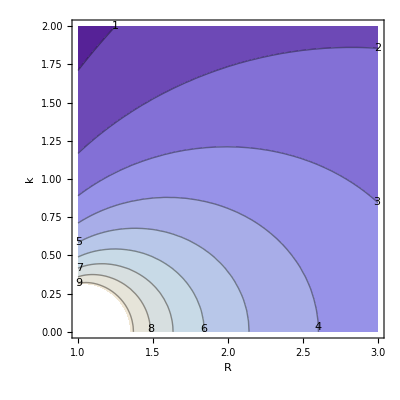

```mathematica
ContourPlot[FillonSum[1,0.2,R,0.05,10,k],{R,1,3},{k,0,2},ContourLabels->True,(*Contours->Table[0.5n,{n,0,40}],*)FrameLabel->Automatic,AspectRatio->2/2]
```

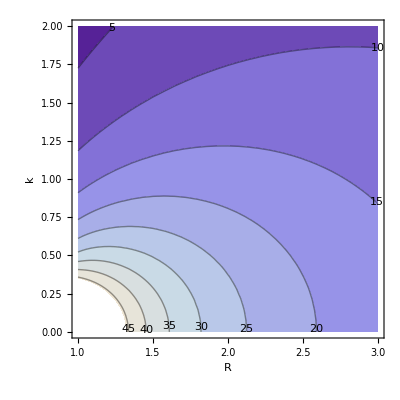

```mathematica
ContourPlot[FillonSum[1,1,R,0.05,10,k],{R,1,3},{k,0,2},ContourLabels->True,(*Contours->Table[0.5n,{n,0,40}],*)FrameLabel->Automatic,AspectRatio->2/2]
```

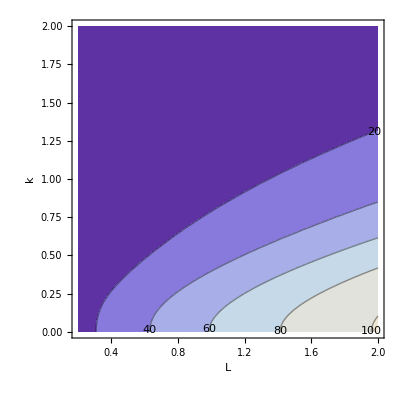

```mathematica
ContourPlot[FillonSum[1,L,1.1,0.05,10,k],{L,0.2,2},{k,0,2},ContourLabels->True,(*Contours->Table[0.5n,{n,0,40}],*)FrameLabel->Automatic,AspectRatio->2/2]
```

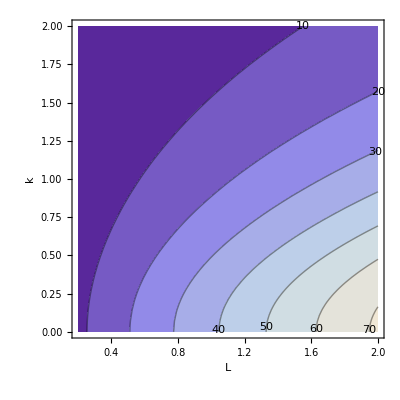

```mathematica
ContourPlot[FillonSum[1,L,1.5,0.05,10,k],{L,0.2,2},{k,0,2},ContourLabels->True,(*Contours->Table[0.5n,{n,0,40}],*)FrameLabel->Automatic,AspectRatio->2/2]
```

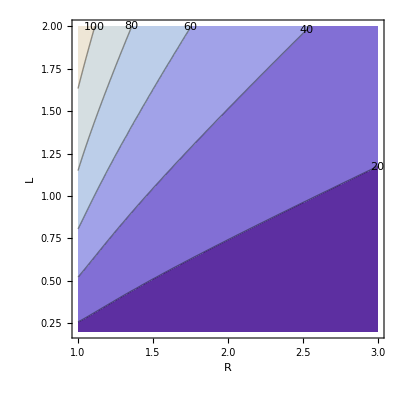

```mathematica
ContourPlot[FillonSum[1,L,R,0.05,10,0],{R,1,3},{L,0.2,2},ContourLabels->True,(*Contours->Table[0.5n,{n,0,40}],*)FrameLabel->Automatic,AspectRatio->2/2]
```

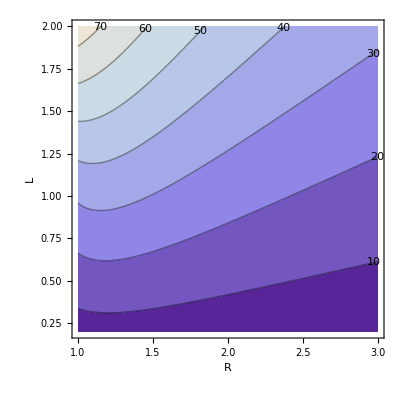

```mathematica
ContourPlot[FillonSum[1,L,R,0.05,10,0.5],{R,1,3},{L,0.2,2},ContourLabels->True,(*Contours->Table[0.5n,{n,0,40}],*)FrameLabel->Automatic,AspectRatio->2/2]
```

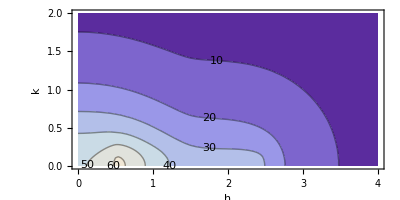

```mathematica
ContourPlot[FilloffSum[1,0.2,1.5,0.05,10,h,k],{h,0,4},{k,0,2},ContourLabels->True,(*Contours->Table[0.5n,{n,0,40}],*)FrameLabel->Automatic,AspectRatio->2/4]
```